```mathematica
dispersion[x_,y_] := -2*(Cos[x]+Cos[y])-4*tp*Cos[x]*Cos[y]
```

```mathematica
tp = -0.35;
mu = 8*(tp-2*tp^3);
```

```mathematica
mu
```

-2.114

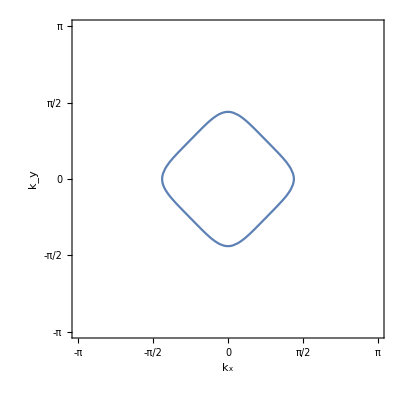

```mathematica
ContourPlot[dispersion[x,y]==mu,{x,-Pi,Pi},{y,-Pi,Pi},Frame->True,FrameStyle->Black,FrameLabel->{"k_x","k_y"},FrameTicks -> {{{-Pi,-Pi/2,0,Pi/2,Pi},None},{{-Pi,-Pi/2,0,Pi/2,Pi},None}}]
```

```mathematica
Solve[dispersion[x,x]==mu,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.795399},{x→0.-1.40327 ⅈ},{x→0.+1.40327 ⅈ},{x→0.795399}}

```mathematica
pt = 0.795399;
```

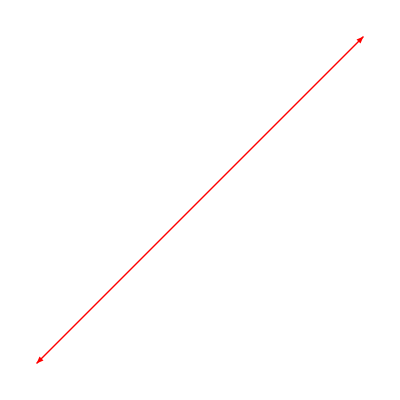

```mathematica
Graphics[{Red,Arrowheads[{-.1,.1}],Arrow[{{-pt,-pt},{pt,pt}}]}]
```

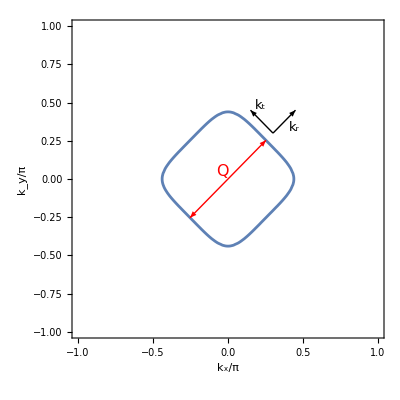

```mathematica
Show[{ContourPlot[dispersion[Pi*x,Pi*y]==mu,{x,-1,1},{y,-1,1},ContourStyle->bl,Frame->True,FrameStyle->Black,FrameLabel->{Style["k_x/π",19,Black,FontFamily->"Times"],Style["k_y/π",19,Black,FontFamily->"Times"]},LabelStyle->Black,FrameTicks -> {Style[{{-1.0,-0.5,0.0,0.5,1.0},None},{{-1,-0.5,0,0.5,1},None}],19}],Graphics[{Red,Arrowheads[{-.05,.05}],Arrow[{{-pt/Pi,-pt/Pi},{pt/Pi,pt/Pi}}],Text[Style["Q",16,FontFamily->"Times"],{-0.04,0.05}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.45,0.45}}],Text[Style["k_r",13,FontFamily->"Times"],{0.44,0.34}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.15,0.45}}],Text[Style["k_t",13,FontFamily->"Times"],{0.22,0.48}]}]}]
```

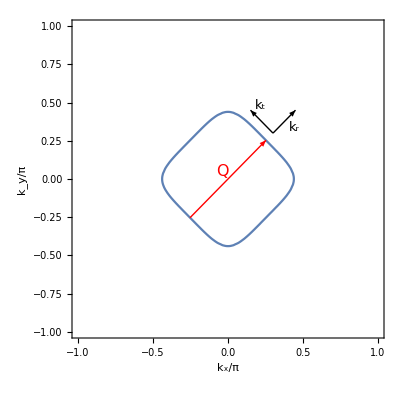

```mathematica
Show[{ContourPlot[dispersion[Pi*x,Pi*y]==mu,{x,-1,1},{y,-1,1},ContourStyle->bl,Frame->True,FrameStyle->Black,FrameLabel->{Style["k_x/π",19,Black,FontFamily->"Times"],Style["k_y/π",19,Black,FontFamily->"Times"]},LabelStyle->Black,FrameTicks -> {Style[{{-1.0,-0.5,0.0,0.5,1.0},None},{{-1,-0.5,0,0.5,1},None}],19}],Graphics[{Red,Arrowheads[{0,.05}],Arrow[{{-pt/Pi,-pt/Pi},{pt/Pi,pt/Pi}}],Text[Style["Q",16,FontFamily->"Times"],{-0.04,0.05}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.45,0.45}}],Text[Style["k_r",13,FontFamily->"Times"],{0.44,0.34}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.15,0.45}}],Text[Style["k_t",13,FontFamily->"Times"],{0.22,0.48}]}]}]
```

```mathematica
background = RGBColor[18/255,18/255,18/255]
whiteColor = RGBColor[221/255,221/255,221/255]
```

RGBColor[Rational[6, 85], Rational[6, 85], Rational[6, 85]]

RGBColor[Rational[13, 15], Rational[13, 15], Rational[13, 15]]

```mathematica
hellblau = RGBColor[86/255,180/255,233/255]
gruen = RGBColor[61/255,155/255,116/255]
sanftgelb = RGBColor[242/255,201/255,76/255]
koralle = RGBColor[242/255,107/255,56/255]
rosa = RGBColor[244/255,143/255,177/255]
bahamagelb=RGBColor[249/255,194/255,0/255]
chartreusegruen = RGBColor[169/255,228/255,0/255]
weichmagenta = RGBColor[255/255,64/255,129/255]
bordeaux = RGBColor[106/255,13/255,61/255]
```

RGBColor[Rational[86, 255], Rational[12, 17], Rational[233, 255]]

RGBColor[Rational[61, 255], Rational[31, 51], Rational[116, 255]]

RGBColor[Rational[242, 255], Rational[67, 85], Rational[76, 255]]

RGBColor[Rational[242, 255], Rational[107, 255], Rational[56, 255]]

RGBColor[Rational[244, 255], Rational[143, 255], Rational[59, 85]]

RGBColor[Rational[83, 85], Rational[194, 255], 0]

RGBColor[Rational[169, 255], Rational[76, 85], 0]

RGBColor[1, Rational[64, 255], Rational[43, 85]]

RGBColor[Rational[106, 255], Rational[13, 255], Rational[61, 255]]

```mathematica
nesting = weichmagenta
```

RGBColor[1, Rational[64, 255], Rational[43, 85]]

```mathematica
Solve[dispersion[x,x]==mu,x][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→-0.795399}

```mathematica
tp = -0.35;
mu = 8*(tp-2*tp^3);
pt = 0.795399
```

0.795399

```mathematica
nesting = sanftgelb
```

RGBColor[Rational[242, 255], Rational[67, 85], Rational[76, 255]]

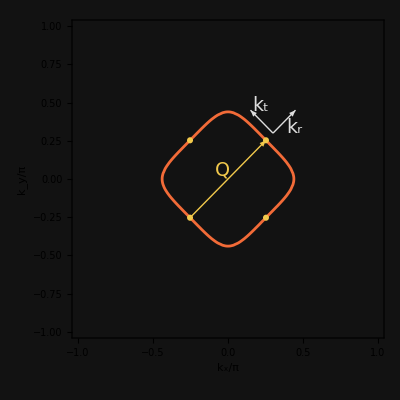

```mathematica
fsPlot=Show[{ContourPlot[dispersion[Pi*x,Pi*y]==mu,{x,-1,1},{y,-1,1},ContourStyle->koralle,Frame->True,FrameStyle->Directive[Thickness[0.003],whiteColor],FrameLabel->{Style["k_x/π",19,FontFamily->"Tempora"],Style["k_y/π",19,FontFamily->"Tempora"]},LabelStyle->whiteColor,FrameTicks -> {Style[{{-1.0,-0.5,0.0,0.5,1.0},None},{{-1,-0.5,0,0.5,1},None}],19},TicksStyle->whiteColor,Background->background],Graphics[{nesting,Arrowheads[{0,.05}],Arrow[{{-pt/Pi,-pt/Pi},{pt/Pi,pt/Pi}}],Text[Style["Q",19,FontFamily->"Tempora"],{-0.04,0.06}]}],Graphics[{nesting,Disk[{-pt/Pi,-pt/Pi},0.02]}],
Graphics[{nesting,Disk[{pt/Pi,pt/Pi},0.02]}],Graphics[{nesting,Disk[{pt/Pi,-pt/Pi},0.02]}],Graphics[{nesting,Disk[{-pt/Pi,pt/Pi},0.02]}],Graphics[{whiteColor,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.45,0.45}}],Text[Style["k_r",19,FontFamily->"Tempora",whiteColor],{0.44,0.34}]}],Graphics[{whiteColor,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.15,0.45}}],Text[Style["k_t",19,FontFamily->"Tempora"],{0.22,0.48}]}]},ImageSize->400]
```

```mathematica
Export["flatNesting_dark.png",fsPlot,ImageSize->600]
```

flatNesting_dark.png

```mathematica
Export["flatNesting_dark.pdf",fsPlot,"PDF","FontEncoding"->"AdobeStandardEncoding"]
```

flatNesting_dark.pdf

```mathematica
tp = -0.2;
mu = 8*(tp-2*tp^3)-1;
```

```mathematica
Solve[dispersion[x,x]==mu,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.763586},{x→0.-2.1326 ⅈ},{x→0.+2.1326 ⅈ},{x→0.763586}}

```mathematica
pt = 0.763586
```

0.763586

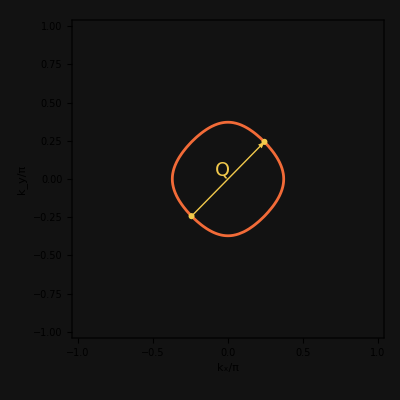

```mathematica
fsPlot=Show[{ContourPlot[dispersion[Pi*x,Pi*y]==mu,{x,-1,1},{y,-1,1},ContourStyle->koralle,Frame->True,FrameStyle->Directive[Thickness[0.003],whiteColor],FrameLabel->{Style["k_x/π",19,FontFamily->"Tempora"],Style["k_y/π",19,FontFamily->"Tempora"]},LabelStyle->whiteColor,FrameTicks -> {Style[{{-1.0,-0.5,0.0,0.5,1.0},None},{{-1,-0.5,0,0.5,1},None}],19},TicksStyle->whiteColor,Background->background],Graphics[{nesting,Arrowheads[{0,.05}],Arrow[{{-pt/Pi,-pt/Pi},{pt/Pi,pt/Pi}}],Text[Style["Q",19,FontFamily->"Tempora"],{-0.04,0.06}]}],Graphics[{nesting,Disk[{-pt/Pi,-pt/Pi},0.02]}],
Graphics[{nesting,Disk[{pt/Pi,pt/Pi},0.02]}](*,Graphics[{whiteColor,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.45,0.45}}],Text[Style["k_r",13,FontFamily->"Times",whiteColor],{0.44,0.34}]}],Graphics[{whiteColor,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.15,0.45}}],Text[Style["k_t",13,FontFamily->"Times"],{0.22,0.48}]}]*)},ImageSize->400]
```

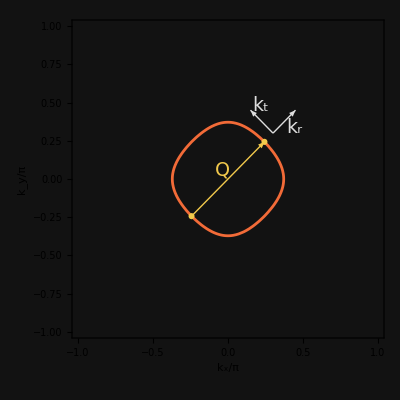

```mathematica
fsPlot=Show[{ContourPlot[dispersion[Pi*x,Pi*y]==mu,{x,-1,1},{y,-1,1},ContourStyle->koralle,Frame->True,FrameStyle->Directive[Thickness[0.003],whiteColor],FrameLabel->{Style["k_x/π",19,FontFamily->"Tempora"],Style["k_y/π",19,FontFamily->"Tempora"]},LabelStyle->whiteColor,FrameTicks -> {Style[{{-1.0,-0.5,0.0,0.5,1.0},None},{{-1,-0.5,0,0.5,1},None}],19},TicksStyle->whiteColor,Background->background],Graphics[{nesting,Arrowheads[{0,.05}],Arrow[{{-pt/Pi,-pt/Pi},{pt/Pi,pt/Pi}}],Text[Style["Q",19,FontFamily->"Tempora"],{-0.04,0.06}]}],Graphics[{nesting,Disk[{-pt/Pi,-pt/Pi},0.02]}],
Graphics[{nesting,Disk[{pt/Pi,pt/Pi},0.02]}],Graphics[{whiteColor,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.45,0.45}}],Text[Style["k_r",19,FontFamily->"Tempora",whiteColor],{0.44,0.34}]}],Graphics[{whiteColor,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.15,0.45}}],Text[Style["k_t",19,FontFamily->"Tempora"],{0.22,0.48}]}]},ImageSize->400]
```